```mathematica
SetDirectory[NotebookDirectory[]];
rawData=Import["NFL.csv"];
{header,data}={rawData[[1]],rawData[[2;;All]]};
```

```mathematica
position=Position[header,"Position"][[1,1]];
weight=Position[header,"Weight (lbs)"][[1,1]];
height=Position[header,"Height (inches)"][[1,1]];
```

```mathematica
positionsID=((data[[All,position]]//DeleteDuplicates)//Sort)[[2;;All]]
```

{C,CB,DB,DE,DL,DT,FB,FS,G,ILB,K,LB,LS,MLB,NT,OG,OL,OLB,OT,P,QB,RB,SAF,SS,T,TE,WR}

```mathematica
positions=data[[All,position]];
weights=data[[All,weight]]*0.453592;
heights=data[[All,height]]*0.0254;
```

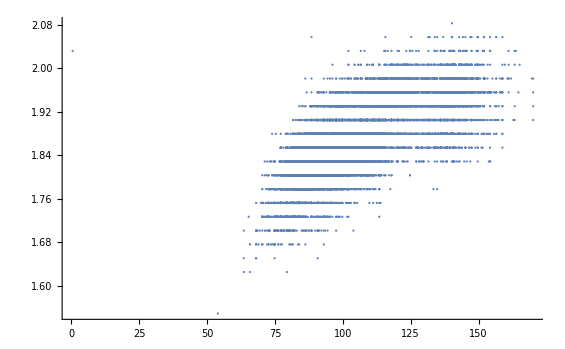

```mathematica
ListPlot[{weights,heights}//Transpose]
```

```mathematica
triplets=Transpose[{heights,weights,positions}];
filtered=Cases[triplets,{a_,b_,c_}/;StringLength[c]≥1];
```

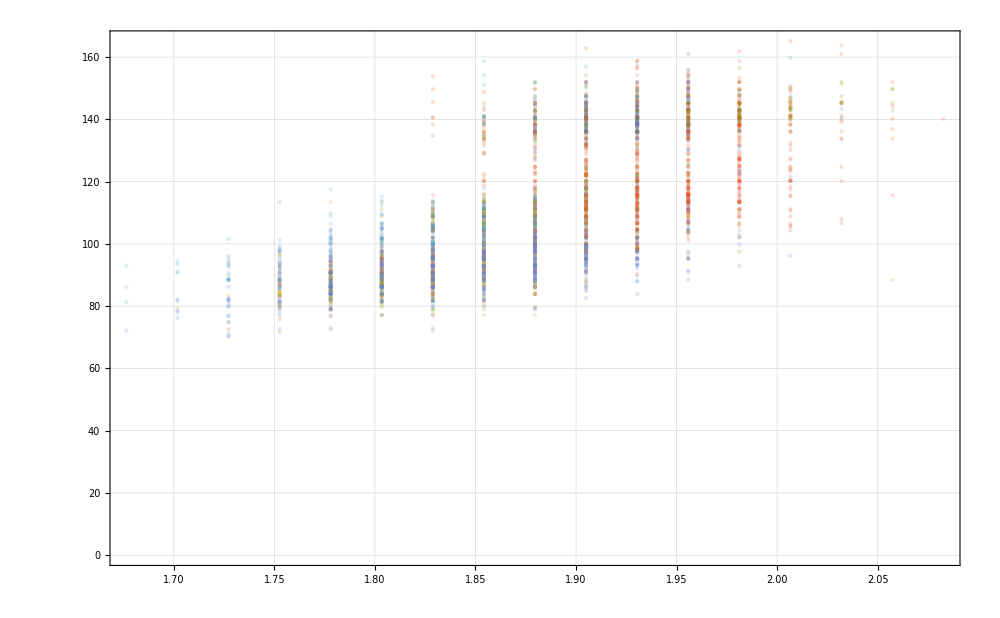

```mathematica
clustered=Map[Cases[filtered,{a_,b_,#}->{a,b}]&,positionsID];
ListPlot[clustered
,Frame->True
,FrameStyle->Thick
,FrameTicksStyle->18
,GridLines->Automatic
,GridLinesStyle->Directive[Gray,Opacity[.15]]
,ImageSize->1000
,PlotStyle->Directive[PointSize[Large],Opacity[.2]]
]
```

```mathematica
clusteredIDs={{"C","LS","OG","OT","NT","T","G","OL","DL","DT","DE"},{"DB","CB","OLB","SAF","SS","FS"},(*{"K","P"},*){"ILB","LB","MLB"},{"QB"},{"RB","FB"},{"TE","WR"}}
```

{{C,LS,OG,OT,NT,T,G,OL,DL,DT,DE},{DB,CB,OLB,SAF,SS,FS},{ILB,LB,MLB},{QB},{RB,FB},{TE,WR}}

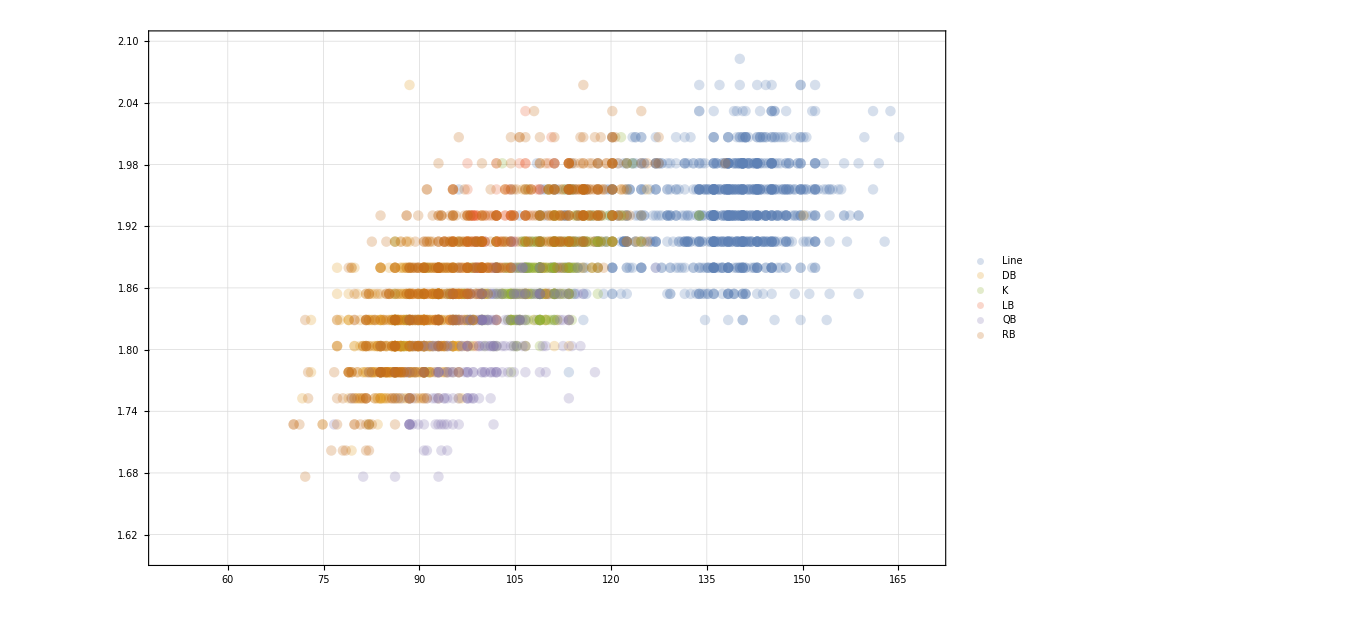

```mathematica
clustered=Map[Cases[filtered,{a_,b_,c_}/;MemberQ[#,c]->{b,a}]&,clusteredIDs];
base=ListPlot[clustered
,Frame->True
,FrameStyle->Thick
,FrameTicksStyle->18
,GridLines->Automatic
,GridLinesStyle->Directive[Gray,Opacity[.15]]
,ImageSize->1000
,PlotRange->{{50,170},{1.6,2.1}}
,PlotLegends->{"Line","DB","K","LB","QB","RB","TE","WR"}
,PlotStyle->Directive[PointSize[.0075],Opacity[.25]]
]
```

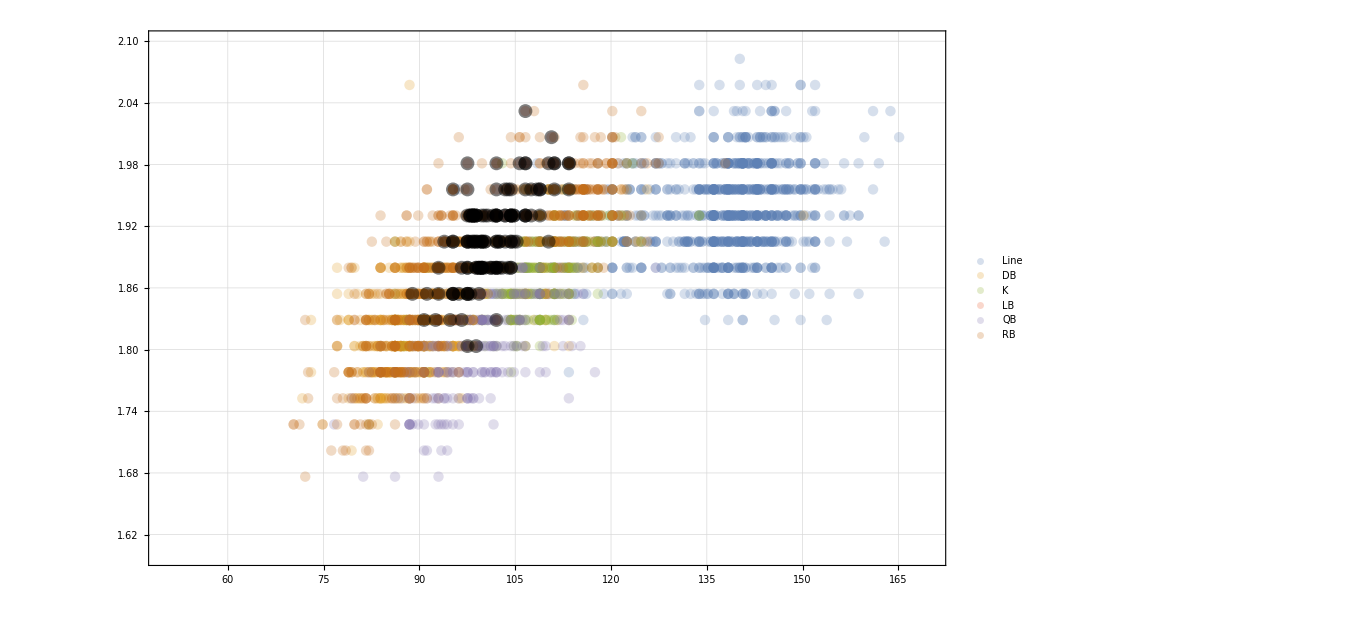

```mathematica
clustered=Map[Cases[filtered,{a_,b_,c_}/;MemberQ[#,c]->{b,a}]&,{{"QB"}}];
layer=ListPlot[clustered
,Frame->True
,FrameStyle->Thick
,FrameTicksStyle->18
,GridLines->Automatic
,GridLinesStyle->Directive[Gray,Opacity[.15]]
,ImageSize->1000
,PlotRange->{{50,170},{1.6,2.1}}
,PlotStyle->Directive[PointSize[.01],Black,Opacity[.5]]
];
Show[base,layer]
```